```mathematica
Needs["NDSolve`FEM`"]
```

# Percentegade difference formula

```mathematica
PercentageDifference[a_, b_]:=Abs[a-b]/Max[a,b]100.;
```

```mathematica
PercentageDifference[100,99]
```

1.

# Circular integration test with better boundaries

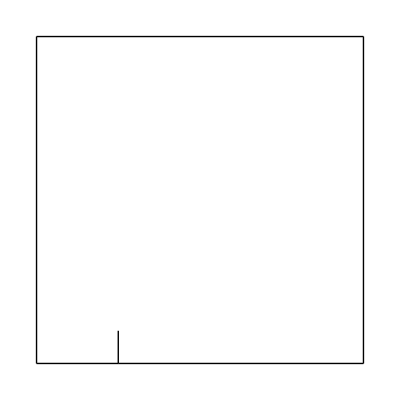

```mathematica
boundary = ToBoundaryMesh[
"Coordinates"->{
{0,0},
{0.25,0},
{0.25,0.1},
{1,0},
{1,1},
{0,1}
},
"BoundaryElements"->{
LineElement[{
{1,2},
{2,3},
{2,4},
{4,5},
{5,6},
{6,1}},
{2,2,2,2,2,2}
]
}
];
reg = ToElementMesh[boundary,
"MeshQualityGoal"->0.7, 
"MaxCellMeasure"->{"Area"->0.01},
MeshRefinementFunction->Function[{vertices,area},(area ≥0.000005Norm[{0.25,0.1}-Mean[vertices]])]
];
boundary["Wireframe"]
```

```mathematica
sol=NDSolveValue[
{
Laplacian[u[x,y],{x,y}]+1==0,
{DirichletCondition[u[x,y]==0,x≤0||x≥1||y≤0||y≥0],
DirichletCondition[u[x,y]==0,x==0.25&&y≥0&&y≤0.1]}
},
u,
{x,y}∈reg,
AccuracyGoal->25,PrecisionGoal->25];
```

```mathematica
Show[
ContourPlot[sol[x,y],{x,y}∈reg],
Graphics[{
Red, Circle[{0.25,0.1},0.1], 
White, Point[{0.25,0.1}]}]
]
```

-Graphics-

#### Now we will integrate in circle

```mathematica
DiskIntegr=NIntegrate[sol[x,y],{x,y}∈Disk[{0.25,0.1},0.1],AccuracyGoal->20,PrecisionGoal->15, MaxRecursion->45]//Quiet
RealDigits[DiskIntegr]
```

0.00046114

{{4,6,1,1,4,0,2,9,3,4,6,8,1,1,2,3},-3}

## Relative difference with FreeFEM

```mathematica
FreeFEMCircleIntegrVal = 0.0004613243016595069;
```

```mathematica
PercentageDifference[0.0004611382344465363, FreeFEMCircleIntegrVal]
```

0.0403333

#### with a little better mesh

```mathematica
PercentageDifference[0.00046114029346811235, FreeFEMCircleIntegrVal]
```

0.0398869

Relative difference is 0.040333%, and with improved mesh(2x smaller mesh elements): 0.0398869%

#### Whole region

```mathematica
FreeFEMREgionIntegrVal=0.03420196874531437;
```

```mathematica
wholeRigIntegr=NIntegrate[sol[x,y],{x,y}∈reg,AccuracyGoal->20,PrecisionGoal->15,MaxRecursion->45]
RealDigits[wholeRigIntegr]
```

0.034202

{{3,4,2,0,2,0,3,3,5,5,5,2,0,0,5,0},-1}

```mathematica
PercentageDifference[0.03420202360857102,FreeFEMREgionIntegrVal]
```

0.000160409

With better mesh(2x smaller mesh element)

```mathematica
PercentageDifference[0.0342020335552005,FreeFEMREgionIntegrVal]
```

0.000189491

relative difference is 0.000160409%, and improved mesh(2x smaller elemts) - 0.000189491%

#### Max Value of function

```mathematica
maxval=NMaxValue[sol[x,y],{x,y}∈reg]//Quiet;
RealDigits[maxval]
Print[maxval]
```

{{7,2,6,3,7,1,1,2,0,8,2,2,3,9,8,0},-1}

0.0726371

# Test With exact implementation like in FreeFem++

```mathematica
BaseVector[nf_Integer, zf_]:=If[Mod[nf,2]==0,-Im[zf^(nf/2.)],Re[zf^(nf/2.)]]
```

### predefined integral

```mathematica
R = 0.01(*same radius is in freefem*);
exponant = 2(*value from FreeFem*);
tipangle = Pi/2;
x0 = 0.25;
y0 = 0.1;

a[order_Integer]:=
NIntegrate[
sol[x,y] 
Exp[-((√((x - 0.25)^2+(y - 0.1)^2))/R)^exponant]
BaseVector[order, 
Exp[-I tipangle] (x-x0 + I(y - y0)) 
],
{x,y}∈Disk[{x0,y0},3R],
AccuracyGoal->20, 
PrecisionGoal->15,
MaxRecursion->50,
WorkingPrecision->16]/
NIntegrate[
Exp[-((√((x - 0.25)^2+(y - 0.1)^2))/R)^exponant]
BaseVector[order, 
Exp[-I tipangle] (x-x0 + I(y - y0)) ]^2,
{x,y}∈Disk[{x0,y0},3R],
AccuracyGoal->20, 
PrecisionGoal->15,
MaxRecursion->50,
WorkingPrecision->16]
```

### And final value check!

```mathematica
FreeFemA1 = 0.1018660081624733;
FreeFemA2 = 0.04546179329449326;
FreeFemA3 = 0.1308697639326795;
```

```mathematica
a[1]
```

0.101884742903876

```mathematica
PercentageDifference[0.10188474290387570859726349359799516302, 0.1018660081624733]
```

0.0183882

Improved mesh(2x smaller element size)

```mathematica
PercentageDifference[a[1], FreeFemA1]
```

0.0217134

#### Relative difference is 0.0183882%. Improved mesh(2x smaller element size) - 0.0217134%.

```mathematica
a[2]
```

0.0454658693471131

```mathematica
PercentageDifference[0.0454658693471130828633, 0.04546179329449326]
```

0.00896508

Improved mesh(2x smaller element size)

```mathematica
PercentageDifference[a[2], FreeFemA2]
```

0.00900529

### Relative difference is 0.00896508%. Improved mesh(2x smaller element size) - 0.00900529%.

```mathematica
a[3]
```

0.131004139092708

```mathematica
PercentageDifference[0.1310041390927083967873, 0.1308697639326795]
```

0.102573

Improved mesh(2x smaller element size)

```mathematica
PercentageDifference[a[3], FreeFemA3]
```

0.102755

### Relative difference is 0.102573%. Improved mesh(2x smaller element size) - 0.102755%.

# RiverSIM comparsion and its optimal parameters

```mathematica
FreeFemA1 = 0.1018660081624733;
FreeFemA2 = 0.04546179329449326;
FreeFemA3 = 0.1308697639326795;
regSize={1,1};
dx = 0.25;
Radius=0.01;
IntegrationRadius=3Radius;
```

# MeshRefinmentFunction

```mathematica
SingleTip[r_, exp_, maxarea_,r0_]:=(1+maxarea-Exp[-(r/r0)^exp]);
```

```mathematica
tipPoints = {{0,0},{1,1},{0.5,1}};
```

```mathematica
Manipulate[
Plot3D[
Min@Map[
SingleTip[Norm[{x,y}-#],exp[[1]],0.0001,exp[[2]]]&, 
{p1,p2,p3}],
{x,0,1},{y,0,1},
PlotRange->All,
PerformanceGoal->"Quality",
PlotTheme->"ZMesh",
PlotPoints->{100,100}],
{exp,{0,0.01},{10,1}},
{p1,{0,0},{1,1}},
{p2,{0,0},{1,1}},
{p3,{0,0},{1,1}},ControlType->Slider2D
]
```

General::munfl: Exp[-745.084] is too small to represent as a normalized machine number; precision may be lost.

## Angle of New Point evaluation Test 30.03

```mathematica
0.0233587,0.0117224
```

```mathematica
-ArcTan[2*0.0117224/0.0233587 √0.01]//RealDigits
```

{{1,0,0,0,3,3,5,8,8,9,3,8,7,1,7,7},0}

```mathematica
Cos[-0.03184168030963936]*0.01
```

0.00999493

```mathematica
Sin[-0.03184168030963936]*0.01
```

-0.000318363

BUT C++ gives -1.4767824476518645 not -0.0318416803!!!! Strange!

```mathematica
-1.4767824476518645
```

0.0940139

```mathematica
Pi/2//N
```

1.5708

```mathematica
ArcTan@-1.4767824476518645
```

-0.975573

```mathematica
ArcTan[√3]
```

π/3

#### What wrong with this?? Polar Model::next_point(vector<double> series_params) { //FIXME: should here be - or +???? double phi = -atan(2 * series_params[2]/series_params[1] * sqrt(ds)); return {ds, phi}; }

#### Indexes was wrong :)